```mathematica
cm = 72/2.54 (*centimetres*);
```

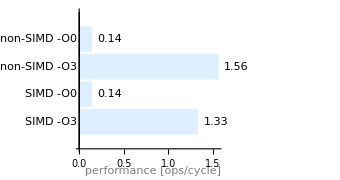

```mathematica
values={0.14, 1.56, 0.14, 1.33};
labels={"non-SIMD -O0", "non-SIMD -O3","SIMD -O0", "SIMD -O3"};
figure2=BarChart[Reverse@Thread[Labeled[values, labels]], 
   ChartLabels -> Placed[Reverse@values, After], BarOrigin -> Left, 
   ChartStyle -> LightBlue, PlotRange -> 4, AspectRatio -> 0.53,  ImagePadding->{{65,0},{30,0}},PlotRangeClipping->False,
   Epilog -> {Line[{{4, 0}, {4, 10}}],Text[Style["peak performance", Gray], {3.27, 4.9}],Text[Style["performance [ops/cycle]",Gray],Offset[{0,-14},Scaled[{1,0}]],{1,1}]}];
Show[figure2, ImageSize -> 12 cm]
```

```mathematica
Reverse[values1~Join~values2]
```

{22.41,63.02,32.41,26.432,18.53,15.83,53.48}

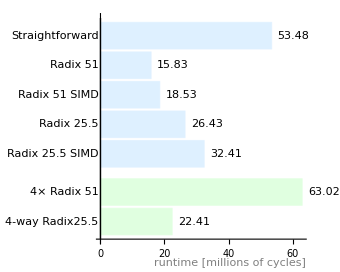

```mathematica
values1={53.48, 15.83, 18.53, 26.43,32.41};
labels1={"Straightforward", "Radix 51","Radix 51 SIMD","Radix 25.5","Radix 25.5 SIMD"};
values2={63.02,22.41};
labels2={"4× Radix 51","4-way Radix25.5"};
figure3=BarChart[{Reverse@Thread[Labeled[values2, labels2]],Reverse@Thread[Labeled[values1, labels1]]}, 
   LabelingFunction->(Placed[#1,After]&), BarOrigin -> Left,
   ChartStyle->{{LightGreen,LightBlue},None}, AspectRatio -> 0.8,ImagePadding->{{73,18},{30,0}},PlotRangeClipping->False,Epilog->{Text[Style["runtime [millions of cycles]",Gray],Offset[{0,-14},Scaled[{1,0}]],{1,1}]}
];
Show[figure3, ImageSize -> 12cm]
```

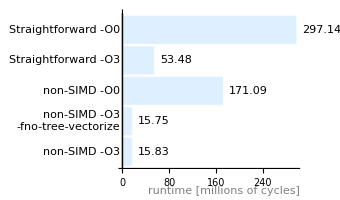

```mathematica
values={297.14, 53.48, 171.09,15.75,15.83};
labels={"Straightforward -O0", "Straightforward -O3", 
  "non-SIMD -O0", Style["non-SIMD -O3\n-fno-tree-vectorize",Small,LineSpacing->{0, 9}], "non-SIMD -O3"};
figure3=BarChart[Reverse@Thread[Labeled[values, labels]], 
   LabelingFunction->(Placed[#1,After]&), BarOrigin -> Left,
   ChartStyle -> LightBlue, AspectRatio -> 0.59,ImagePadding->{{85,25},{30,0}},PlotRangeClipping->False,Epilog->{Text[Style["runtime [millions of cycles]",Gray],Offset[{0,-14},Scaled[{1,0}]],{1,1}]}];
Show[figure3, ImageSize -> 12cm]
```

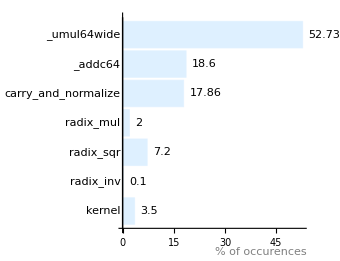

```mathematica
values={52.73,18.6,17.86,2,7.2,0.1,3.5};
labels={"_umul64wide",
"_addc64",
"carry_and_normalize",
"radix_mul",
"radix_sqr",
"radix_inv",
"kernel"};
figure4=BarChart[Reverse@Thread[Labeled[values, labels]], 
   LabelingFunction->(Placed[#1,After]&), BarOrigin -> Left,PlotRange->60,
   ChartStyle -> LightBlue, AspectRatio -> 0.77,ImagePadding->{{91,0},{30,0}},PlotRangeClipping->False,Epilog->{Text[Style["% of occurences",Gray],Offset[{0,-14},Scaled[{1,0}]],{1,1}]}];
Show[figure4, ImageSize -> 12cm]
```

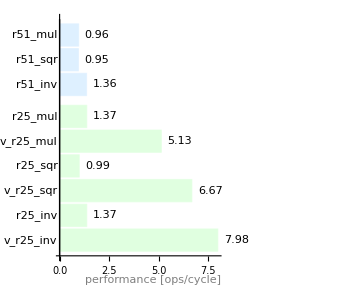

```mathematica
values1={0.96,0.95,1.36};
labels1={"r51_mul", "r51_sqr","r51_inv"};
values2={1.37,5.13,0.99,6.67,1.37,7.98};
labels2={"r25_mul","v_r25_mul","r25_sqr","v_r25_sqr","r25_inv","v_r25_inv"};
figure3=BarChart[{Reverse@Thread[Labeled[values2, labels2]],Reverse@Thread[Labeled[values1, labels1]]}, 
   LabelingFunction->(Placed[#1,After]&), BarOrigin -> Left,PlotRange->13,
   ChartStyle->{{LightGreen,LightBlue},None}, AspectRatio -> 0.85,ImagePadding->{{43,0},{30,0}},PlotRangeClipping->False,Epilog->{Line[{{13, 0}, {13, 10}}],Text[Style["SIMD peak performance", Gray], {10.1, 9.8}],Text[Style["performance [ops/cycle]",Gray],Offset[{0,-14},Scaled[{1,0}]],{1,1}]}
];
Show[figure3, ImageSize -> 12cm]
```